```mathematica
Clear["Global`*"]
```

```mathematica
pA={a*Cos[t],0};pB={0,a*Sin[t]};
pAB=pB-pA;
```

```mathematica
pABr=RotationMatrix[-Pi/2].pAB;
pD=pABr+pA;
{xt,yt}=pD
```

{a Cos[t]+a Sin[t],a Cos[t]}

```mathematica
(xt-yt)^2+yt^2-a^2//FullSimplify
```

0

```mathematica
aa=5;
```

```mathematica
solxy=Solve[(x-y)^2+y^2==aa^2,Integers];
pt={x,y}/.solxy
```

{{-7,-4},{-7,-3},{-5,-5},{-5,0},{-1,-4},{-1,3},{1,-3},{1,4},{5,0},{5,5},{7,3},{7,4}}

```mathematica
ptpoly={{5,0},{7,3},{7,4},{5,5},{1,4},{-1,3},{-5,0},{-7,-3},{-7,-4},{-5,-5},{-1,-4},{1,-3}}
```

{{5,0},{7,3},{7,4},{5,5},{1,4},{-1,3},{-5,0},{-7,-3},{-7,-4},{-5,-5},{-1,-4},{1,-3}}

```mathematica
g1=ParametricPlot[{aa*Cos[t]+aa*Sin[t],aa*Cos[t]},{t,0,2*Pi},GridLines->{Table[i,{i,-8,8,2}],Table[j,{j,-8,8,2}]},Ticks->{Table[i,{i,-8,8,2}],Table[j,{j,-8,8,2}]},PlotRange->{{-8,8},{-8,8}},PlotStyle->Thickness[0.006],AspectRatio->Automatic,ImageSize->Large];
```

```mathematica
g2=Graphics[{EdgeForm[{Thick,Orange}],FaceForm[],Translate[Rotate[Rectangle[{0,0},{aa,aa}],-Pi/4,{0,0}],{0,aa/Sqrt[2]}]}];
```

```mathematica
g3=Graphics[{Thick,EdgeForm[{Thick,Orange}],FaceForm[White],Disk[{(aa+aa)/Sqrt[2],aa/Sqrt[2]},0.08]}];
```

```mathematica
g4=Graphics[{PointSize[0.015],Black,Point[pt],
Opacity[0.4],EdgeForm[{Thick,Gray}],LightGray,Polygon[ptpoly]}];
```

```mathematica
g5=Graphics[{Text[Style["O",FontFamily->"Times New Roman",Italic,20],{-0.3,-0.3}],
Text[Style["A",FontFamily->"Times New Roman",Italic,20],{3.5,-0.3}],
Text[Style["B",FontFamily->"Times New Roman",Italic,20],{-0.3,3.7}],
Text[Style["C",FontFamily->"Times New Roman",Italic,20],{3.3,7.2}],
Text[Style["D",FontFamily->"Times New Roman",Italic,20],{7.5,3.5}]}];
```

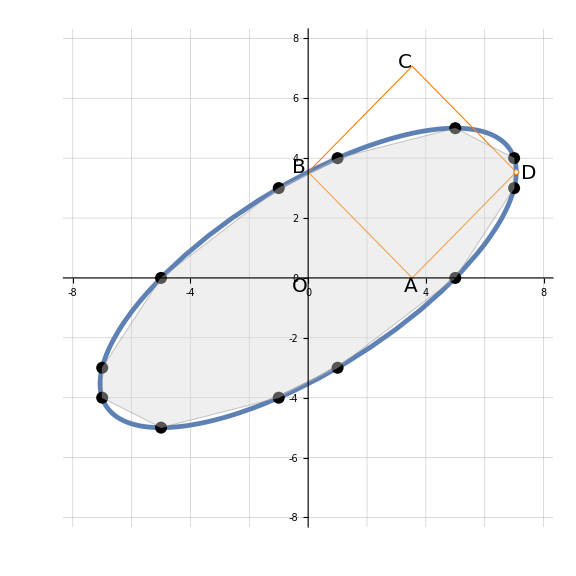

```mathematica
Show[g1,g2,g3,g4,g5]
```